## Playing with Wolfram’s Twitter Capabilities

## Big-T

Status as of July 1, 2017.

#### Let’s look at some basic info:

```mathematica
twitter=ServiceConnect["Twitter","New"]
```

ServiceObject[…]

```mathematica
twitter["UserData","Username"->"realDonaldTrump"]
```

{<|ID→25073877,Name→Donald J. Trump,ScreenName→realDonaldTrump,Location→Washington, DC,FollowersCount→33179562,FriendsCount→45,FavouritesCount→24|>}

33 MILLION PEOPLE.

#### What are his favorite words?

```mathematica
getTweetStrings[username_,number_:4000]:=Block[{text,tweetsDT},
tweetsDT=twitter["TweetList","Username"->username,MaxItems->number];
text=Flatten[StringSplit[Normal[tweetsDT[All,"Text"]]],1];
StringDelete[DeleteStopwords[text],{"&amp",";",".",",","-","_","\"","(",")","RT"}]]
```

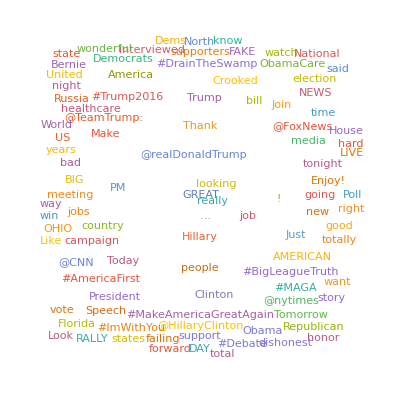

```mathematica
WordCloud@getTweetStrings["realDonaldTrump"]
```

Looks GREAT

```mathematica
dttweetsstrings=getTweetStrings["realDonaldTrump"];
Total@StringCount[dttweetsstrings,{"Great","great","GREAT"}]
```

556

#### Bigly Positive

```mathematica
posneg=Classify["Sentiment",dttweetsstrings];
```

```mathematica
tallied=Transpose@Tally@posneg
```

{{Negative,Neutral,Positive,Indeterminate},{6608,6245,21606,224}}

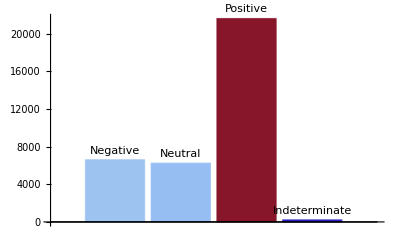

```mathematica
BarChart[tallied[[2]],ChartLabels->Placed[tallied[[1]],Above],ColorFunction->"ThermometerColors"]
```

The ~15,000 difference is yuge.

#### Who’s his posse?

```mathematica
posse=twitter["Friends","Username"->"realDonaldTrump"]
```

{Tucker Carlson,Jesse Watters,The White House,Dan Scavino Jr.,Kellyanne Conway,Reince Priebus,Roma Downey,Trump Organization,Trump Golf,Tiffany Ariana Trump,Laura Ingraham,Mike Pence,Official Team Trump,DRUDGE REPORT,Vanessa Trump,Lara Trump,Sean Hannity,Fox Nation,Corey R. Lewandowski,Ann Coulter,Diamond and Silk®,KATRINA CAMPINS,Katrina Pierson,Michael Cohen,FOX & friends,MELANIA TRUMP,Geraldo Rivera,Eric Bolling,Mark Burnett,Gary Player,Vince McMahon,Dan Scavino Jr.,Trump Waikiki,Trump National Doral,Trump Charlotte,Trump Vegas Hotel,Trump Hotel Chicago,Trump Washington DC,Trump Los Angeles,Eric Trump,Bill O'Reilly,Greta Van Susteren,Piers Morgan,Donald Trump Jr.,Ivanka Trump}

```mathematica
possegraph=twitter["FriendNetwork","Username"->"realDonaldTrump"];
```

ServiceExecute::rlim: The request limit for this resource has been reached for the current rate limit window. Please try again in a few minutes.

```mathematica
CommunityGraphPlot[possegraph]
```

-Graphics-

Three big clumps. He’s one of the red ones, can you guess which? Unfortunately, I wasn’t able to get the vertex names to show on the graph without hovering over each one since the vertex list and friend list aren’t in the same order.

```mathematica
VertexList[possegraph]
```

{25073877,22703645,56561449,822215673812119553,823367015830323201,471672239,20733972,322293052,720293443260456960,2325495378,245963716,50769180,22203756,729676086632656900,14669951,475802156,75541946,41634520,37764422,4121225056,196168350,2908170952,34852681,25429371,52136185,15513604,108471631,246500501,14839147,316865635,26829777,1222639789,620571475,119157187,633797941,726414091,82504071,48223726,1013672084,29562422,39349894,23970102,16031927,216299334,39344374,52544275}

Note that Big-T’s ID is 25073877 whereas Tucker’s is 22703645.

How much do his friends reply?

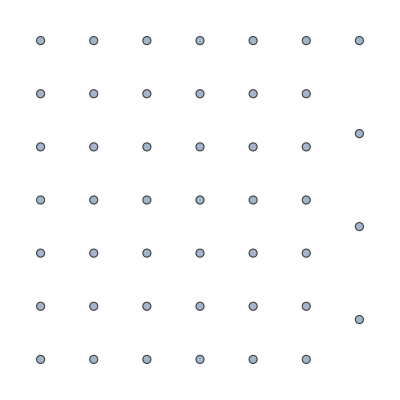

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
twitter["FriendReplyToNetwork","Username"->"realDonaldTrump"]
```

None of his friends reply to him or each other apparently.

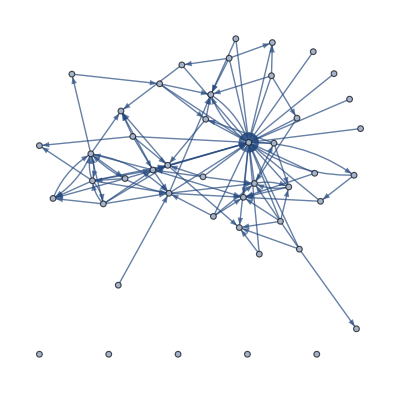

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
twitter["FriendMentionNetwork","Username"->"realDonaldTrump"]
```

They do like to gossip about one another though. Big-T’s node in this graph is fairly obvious.

#### When does he use Twitter?

```mathematica
dteventseries=twitter["TweetEventSeries","Username"->"realDonaldTrump",MaxItems->5000]
```

EventSeries[…]

```mathematica
datediff=DateDifference[DateObject[{2016, 5, 21}],DateObject[{2017, 7, 2}]]
```

407 days

He’s had the account since 2009, however Twitter seems to delete tweets after a certain number or time frame. The real number of tweets is upwards of 35,000.

```mathematica
N[Quantity[Length@dteventseries["Times"],"tweets"]/datediff]
```

7.90909 tweets/day

Eight a day is too many for anyone.

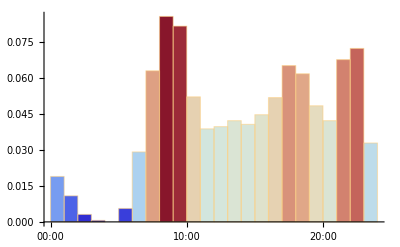

```mathematica
hourlypercents=DateHistogram[dteventseries["Dates"],"Hour","Probability",DateReduction->"Day",ColorFunction->"ThermometerColors"]
```

He sure does like his morning and night tweet sessions

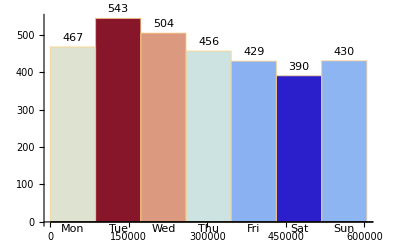

```mathematica
weekcounts=DateHistogram[dteventseries["Dates"],"Day",DateReduction->"Week",ColorFunction->"ThermometerColors",LabelingFunction->Above]
```

Tuesday’s tweet hustle day. In all honesty though, he’s pretty consistent.

And finally, we have the tweet count chart going back to about May 2016.

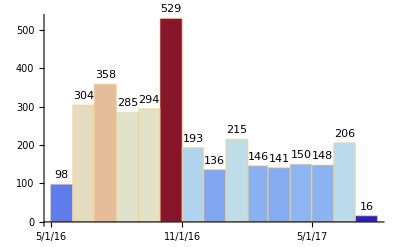

```mathematica
alltimecounts=DateHistogram[dteventseries["Dates"],"Month",ColorFunction->"ThermometerColors",LabelingFunction->Above]
```

The election season spike was expected, but wow that’s a lot.

I regret that I couldn’t look at more of the data since Twitter caps the request amount, although I still had fun with the ~3,200 tweets to which I did have access.